```mathematica
lineintegral = ListPointPlot3D[Table[{t^3,t,t^3},{t,0,2,0.01}],Filling->0]
```

-Graphics3D-

```mathematica
integralgraphic=ParametricPlot3D[{t,2t,t*Exp[2t*z]},{t,0,1},{z,0,3},BoundaryStyle->Directive[Thin,Black],BoxRatios->{1,1,1/2},PlotStyle->Opacity[.5],PlotRange->All]
```

-Graphics3D-

```mathematica
xygraphic=Plot3D[0,{x,0,2},{y,0,2},PlotStyle->Opacity[.2],MeshStyle->Opacity[.2]]
```

-Graphics3D-

```mathematica
Show[integralgraphic,xygraphic,ImageSize->Full,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
problem1 = ParametricPlot3D[{t^3,t,z*t^3},{t,0,1},{z,0,1},BoundaryStyle->Directive[Thin,Black],BoxRatios->{1,1,1/2},PlotStyle->Opacity[.5],PlotRange->All]
```

-Graphics3D-

```mathematica
Show[problem1,xygraphic,ImageSize->Full,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
problem3 = ParametricPlot3D[{4Cos[t],4Sin[t],z*(4Sin[t])^4},{t,-3π/2,π/2},{z,0,1},BoundaryStyle->Directive[Thin,Black],BoxRatios->{1,1,1/2},PlotStyle->Opacity[.5], MeshStyle->RGBColor[0, 0.24, 0.36], PlotRange->All]
```

-Graphics3D-

```mathematica
xygraphic3=Plot3D[0,{x,-4,4},{y,-4,4},PlotStyle->Opacity[.2],MeshStyle->Opacity[.2]]
```

-Graphics3D-

```mathematica
Show[problem3,xygraphic3,ImageSize->Full,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
problem6 = ParametricPlot3D[{t,Log[t],z*t^2},{t,1,E},{z,0,1},BoundaryStyle->Directive[Thin,Black],BoxRatios->{1,1,1/2},PlotStyle->Opacity[.5],PlotRange->All]
```

-Graphics3D-

```mathematica
xygraphic6=Plot3D[0,{x,0,E},{y,0,1},PlotStyle->Opacity[.2],MeshStyle->Opacity[.2]]
```

-Graphics3D-

```mathematica
Show[problem6,xygraphic6,ImageSize->Full,AxesLabel->{x,y,z}]
```

-Graphics3D-

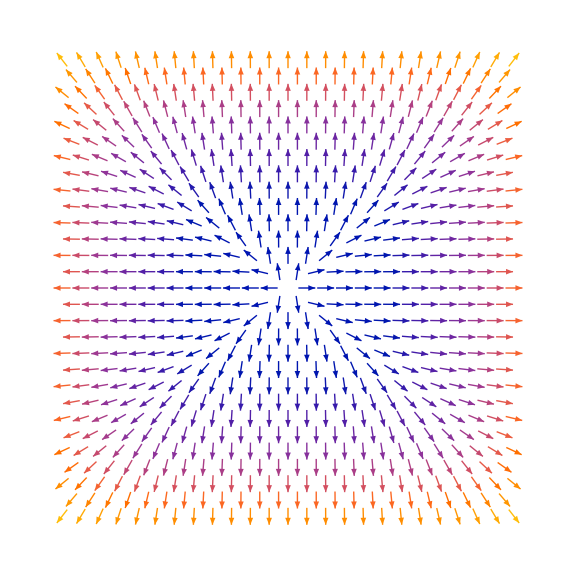

```mathematica
vectorplottest=VectorPlot[{4x^3,5y^3},{x,-4,4},{y,-4,4},Frame->False,VectorStyle->{Black},Background->None,VectorPoints->Fine,ImageSize->Large]
```

```mathematica
testproblem = ParametricPlot3D[{Cos[t],Sin[t],z*(Cos[t]^2+Sin[t]^2)},{t,0,2π},{z,0,1},BoundaryStyle->Directive[Thin,Black],BoxRatios->{1,1,1/2},PlotStyle->Opacity[.5], MeshStyle->RGBColor[0, 0.24, 0.36], PlotRange->All]
```

-Graphics3D-

```mathematica
|
```

```mathematica
testxygraphic=Plot3D[0,{x,-1,1},{y,-1,1},PlotStyle->Opacity[.2],MeshStyle->Opacity[.2]]

testfullgraphic=Plot3D[Sin[x]^2 + Cos[y]^2,{x,-1,1},{y,-1,1},PlotStyle->Opacity[.15],PlotStyle->Opacity[.15]]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[testproblem, testxygraphic,testfullgraphic,ImageSize->Full,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
#Ch16Pr19
```

#Ch16Pr19

```mathematica
xygraphic19=Plot3D[0,{x,0,1},{y,0,1},PlotStyle->Opacity[.2],MeshStyle->Opacity[0], ColorFunction->"Rainbow"]
```

-Graphics3D-

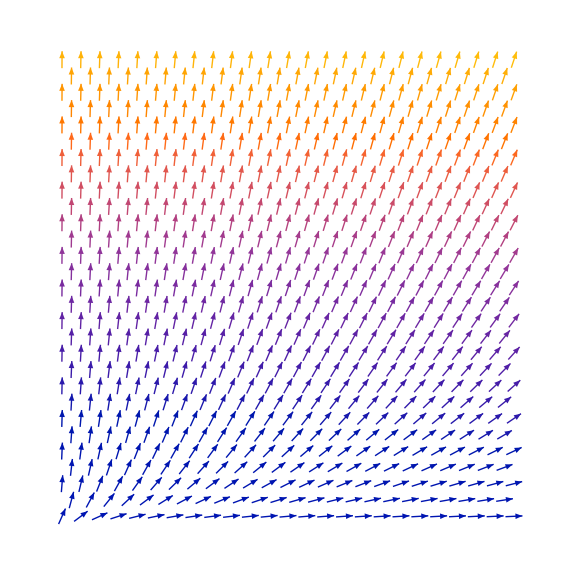

```mathematica
vectorplot19=VectorPlot[{x*y,3y^2},{x,0,1},{y,0,1},Frame->False,VectorStyle->{Black},Background->None,VectorPoints->Fine,ImageSize->Large]
```

```mathematica
slopetexture=Texture@ImageData@RemoveBackground@Rasterize[vectorplot19]
```

Texture[{{{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},564,{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.}},574,{1}}]
 |  |  |  |

```mathematica
slopegraphic=Graphics3D[{slopetexture19,xysquare19},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
integralgraphic=ParametricPlot3D[{11t^4,t^3,z},{t,0,1},{z,0,1},BoundaryStyle->Directive[Thick,Black],PlotStyle->Opacity[.5]]
```

-Graphics3D-

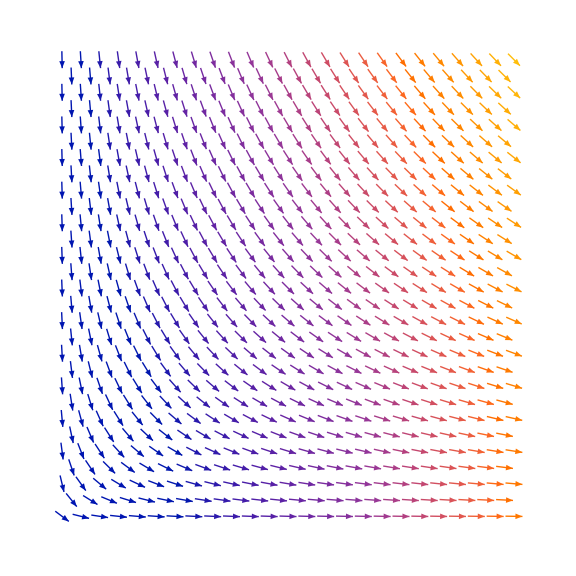

```mathematica
vectorplotex=VectorPlot[{x^2,-x*y},{x,0,1},{y,0,1},Frame->False,VectorStyle->{Black},Background->None,VectorPoints->Fine,ImageSize->Large]
```

```mathematica
slopetextureex=Texture@ImageData@RemoveBackground@Rasterize[vectorplotex]
```

Texture[{{{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},564,{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.}},574,{1}}]
 |  |  |  |

```mathematica
slopegraphic=Graphics3D[{slopetextureex,xysquare19},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
integralgraphicex=ParametricPlot3D[{Cos[t],Sin[t],z(-2*Cos[t]^2*Sin[t])},{t,0,π/2},{z,0,1},
BoundaryStyle->Directive[Thick,Black],PlotStyle->Opacity[.5]]
```

-Graphics3D-

```mathematica
fullgraphicex=Plot3D[Cos[x]^2+Sin[y]^2,{x,0,π/2},{y,0,π/2},PlotStyle->Opacity[.15],PlotStyle->Opacity[.15]]
```

```mathematica
-Graphics3D-
Show[integralgraphicex,xygraphic19, ImageSize->Full, PlotRange->All,ImageSize->Full,BoxRatios->{1,1,1/2},Axes->True,AxesLabel->{x,y,z}]
```

-Graphics3D-

-Graphics3D-

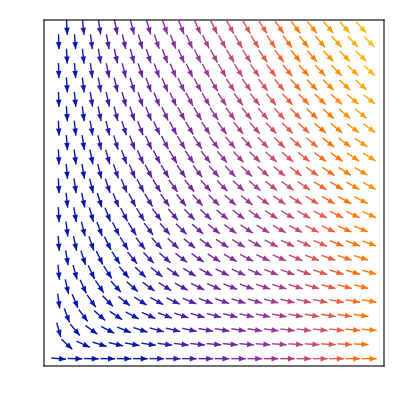

```mathematica
gradientex = VectorPlot[{x^2, -x*y}, {x, 0, 2}, {y, 0, 2},
ColorFunction->"DarkRainbow", VectorPoints->20, FrameTicks->None]
```

```mathematica
textureex = Graphics3D[{Texture[gradientex],Polygon[{{0,0,-0.9},{1,0,-0.9},{1,1,-0.9},{0,1,-0.9}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Show[integralgraphicex,xygraphic19, textureex, ImageSize->Full, PlotRange->All,ImageSize->Full,BoxRatios->{1,1,1/2},Axes->True,AxesLabel->{x,y,z}, PlotStyle->Opacity[.2]]
```

-Graphics3D-

```mathematica
#Chapter16Problem19
```

```mathematica
vectorplot19=VectorPlot[{x*y,3y^2},{x,0,1},{y,0,1},Frame->False,VectorStyle->{Black},Background->None,VectorPoints->Fine,ImageSize->Large]
```

-Graphics-

```mathematica
slopegraphic=Graphics3D[{slopetexture19,xysquare19},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
integralgraphic19=ParametricPlot3D[{11t^4,t^3,z(484t^10+9t^8)},{t,0,1},{z,0,1},
BoundaryStyle->Directive[Thick,Black],PlotStyle->Opacity[.5]]
```

```mathematica
-Graphics3D-
integralgraphic19
```

-Graphics3D-

-Graphics3D-

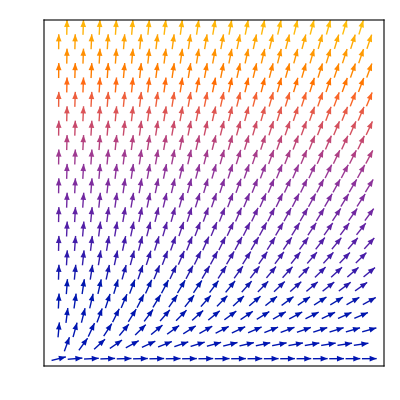

```mathematica
gradient19 = VectorPlot[{x*y, 3y^2}, {x, 0, 1}, {y, 0, 1},
ColorFunction->"DarkRainbow", VectorPoints->20, FrameTicks->None]
```

```mathematica
textureex = Graphics3D[{Texture[gradient19],Polygon[{{0,0,-0.9},{1,0,-0.9},{1,1,-0.9},{0,1,-0.9}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Show[xygraphic19, texture19, integralgraphic19, ImageSize->Full, PlotRange->All,ImageSize->Full,BoxRatios->{1,1,1},Axes->True,AxesLabel->{x,y,z}, PlotStyle->Opacity[.2]]
```

Show::gcomb: Could not combine the graphics objects in Show[xygraphic19,texture19,,ImageSize→Full,PlotRange→All,ImageSize→Full,BoxRatios→{1,1,1},Axes→True,AxesLabel→{x,y,z},PlotStyle→Opacity[0.2]].

Show[xygraphic19,texture19,-Graphics3D-,ImageSize→Full,PlotRange→All,ImageSize→Full,BoxRatios→{1,1,1},Axes→True,AxesLabel→{x,y,z},PlotStyle→Opacity[0.2]]

```mathematica
#Chapter164

#Problem12
```

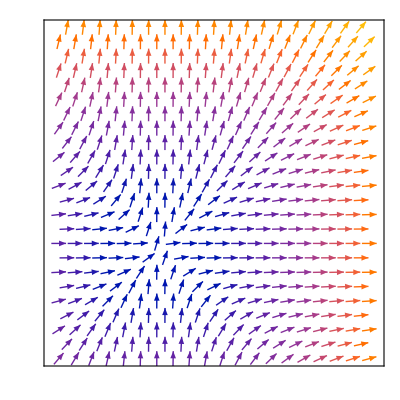

```mathematica
gradient12 = VectorPlot[{x^2, y^2}, {x, -1, 2}, {y, -1, 2},
ColorFunction->"DarkRainbow", VectorPoints->20, FrameTicks->None]
```

```mathematica
texture12 = Graphics3D[{Texture[gradient12],Polygon[{{-1,0,-0.9},{2,0,-0.9},{2,8,-0.9},{-1,8,-0.9}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"]
```

-Graphics3D-

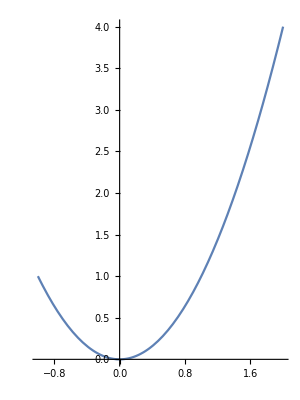

```mathematica
ParametricPlot[{t, t^2}, {t, -1, 2}]
```

```mathematica
integralgraphic12=ParametricPlot3D[{t,t^2,z(2t^5 + t^2)},{t,-1,2},{z,0,1},
BoundaryStyle->Directive[Thick,Black],PlotStyle->Opacity[.5]]
```

-Graphics3D-

```mathematica
xygraphic19=Plot3D[0,{x,-1,2},{y,0,8},PlotStyle->Opacity[.2],MeshStyle->Opacity[0]]
```

-Graphics3D-

```mathematica
Show[integralgraphic12,xygraphic12, texture12, ImageSize->Full, PlotRange->All,ImageSize->Full,BoxRatios->{1,1,1/2},Axes->True,AxesLabel->{x,y,z}, PlotStyle->Opacity[.2]]
```

```mathematica
-Graphics3D-

#Problem13
```

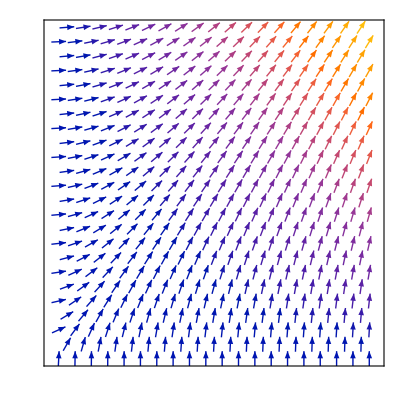

```mathematica
gradient13 = VectorPlot[{x*y^2, x^2*y}, {x, 0, 1.5}, {y, 0, 1.2},
ColorFunction->"DarkRainbow", VectorPoints->20, FrameTicks->None]
```

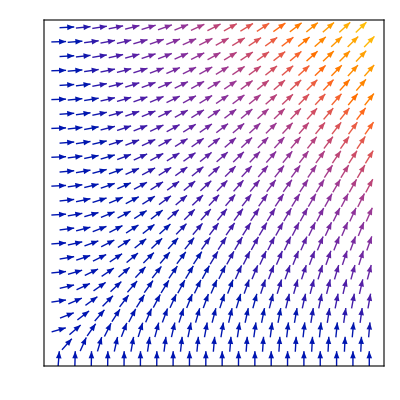
```mathematica
-Graphics-
texture13 = Graphics3D[{Texture[gradient13],Polygon[{{0,0,-0.9},{1.5,0,-0.9},{1.5,1.2,-0.9},{0,1.2,-0.9}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"]
```

-Graphics-

-Graphics3D-

```mathematica
xygraphic13=Plot3D[0,{x,0,1.5},{y,0,1.2},PlotStyle->Opacity[.2],MeshStyle->Opacity[0]]
```

-Graphics3D-

```mathematica
integralgraphic13=ParametricPlot3D[{t + 0.5Sin[0.5*π*t],t+ Cos[0.5*π*t],z(((t + 0.5Sin[0.5*π*t]))^2+(t+ Cos[0.5*π*t])^2)},{t,0,1},{z,0,1},
BoundaryStyle->Directive[Thick,Black],PlotStyle->Opacity[.5]]
```

-Graphics3D-

```mathematica
Show[integralgraphic13,xygraphic13, texture13, ImageSize->Full, PlotRange->All,ImageSize->Full,BoxRatios->{1,1,1/2},Axes->True,AxesLabel->{x,y,z}, PlotStyle->Opacity[.2]]
```

```mathematica
-Graphics3D-
#Problem14
```

```mathematica
xygraphic1=Plot3D[0,{x,-2,2},{y,-2,2},PlotStyle->Opacity[.2],MeshStyle->Opacity[0]]
```

-Graphics3D-

```mathematica
integralgraphic1=ParametricPlot3D[{2Cos[t],2Sin[t],z(4(Cos[t]+Sin [t])Cos[t]-4(Cos[t]-Sin[t])Sin[t])},{t,0,2π},{z,0,1},
BoundaryStyle->Directive[Thick,Black],PlotStyle->Opacity[.5]]
```

-Graphics3D-

```mathematica
Show[integralgraphic1,xygraphic1, ImageSize->Full, PlotRange->All,ImageSize->Full,BoxRatios->{1,1,1/2},Axes->True,AxesLabel->{x,y,z}, PlotStyle->Opacity[.2]]
```

-Graphics3D-